```mathematica
"XMat" Material Systems for Extreme Environments
```

```mathematica
dataGet[str_String,page_]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
parseData2[dataIn_]:=ToLowerCase@DeleteStopwords@Flatten@TextWords@Table[DeleteCases[Cases[dataRaw,XMLElement["a",_,_],Infinity][[i]],XMLElement["b",_,_],Infinity][[3]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
parseData1[dataIn_]:=DeleteStopwords@Flatten@TextWords@Table[Cases[dataIn,XMLElement["a",_,_],Infinity][[i]][[3]][[1]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
associate[words_]:=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];

commonAssociateMinus[dataParsed_,Ncommonest_,minusWords_]:=associate[DeleteCases[Commonest[dataParsed,Ncommonest],minusWords]]
```

```mathematica
dataGet2[page_]:=Table[Block[{url},url="https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&oq=XMat+Material+Systems+for+Extreme+Environments&gs_l=psy-ab.3...125064.126530.0.126806.2.2.0.0.0.0.123.242.0j2.2.0.foo%2Cnso-ehuqi%3D1%2Cnso-ehuui%3D1%2Cewh%3D0%2Cnso-mplt%3D2%2Cnso-enksa%3D0%2Cnso-enfk%3D1%2Cnso-usnt%3D1%2Cnso-qnt-npqp%3D0-1701%2Cnso-qnt-npdq%3D0-54%2Cnso-qnt-npt%3D0-1%2Cnso-qnt-ndc%3D300%2Ccspa-dspm-nm-mnp%3D0-05%2Ccspa-dspm-nm-mxp%3D0-125%2Cnso-unt-npqp%3D0-17%2Cnso-unt-npdq%3D0-54%2Cnso-unt-npt%3D0-0602%2Cnso-unt-ndc%3D300%2Ccspa-uipm-nm-mnp%3D0-007525%2Ccspa-uipm-nm-mxp%3D0-052675%2Ccfro%3D1...0...1.1.64.psy-ab..0.0.0.nELCKH2Q5oo";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
```

```mathematica
dataGet2[1]
```

$CharacterEncoding::utf8: The byte sequence {252} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {246} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {228,104} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

{{}}

```mathematica
url="https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&oq=XMat+Material+Systems+for+Extreme+Environments&gs_l=psy-ab.3...125064.126530.0.126806.2.2.0.0.0.0.123.242.0j2.2.0.foo%2Cnso-ehuqi%3D1%2Cnso-ehuui%3D1%2Cewh%3D0%2Cnso-mplt%3D2%2Cnso-enksa%3D0%2Cnso-enfk%3D1%2Cnso-usnt%3D1%2Cnso-qnt-npqp%3D0-1701%2Cnso-qnt-npdq%3D0-54%2Cnso-qnt-npt%3D0-1%2Cnso-qnt-ndc%3D300%2Ccspa-dspm-nm-mnp%3D0-05%2Ccspa-dspm-nm-mxp%3D0-125%2Cnso-unt-npqp%3D0-17%2Cnso-unt-npdq%3D0-54%2Cnso-unt-npt%3D0-0602%2Cnso-unt-ndc%3D300%2Ccspa-uipm-nm-mnp%3D0-007525%2Ccspa-uipm-nm-mxp%3D0-052675%2Ccfro%3D1...0...1.1.64.psy-ab..0.0.0.nELCKH2Q5oo";
url2="https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&ei=dPOuWbm6NITgadXNtPAJ&start=10&sa=N&biw=1440&bih=755"
url3="https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&ei=dPOuWbm6NITgadXNtPAJ&start=10&sa=N&biw=1440&bih=755"
```

https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&ei=dPOuWbm6NITgadXNtPAJ&start=10&sa=N&biw=1440&bih=755

https://www.google.de/search?q=XMat+Material+Systems+for+Extreme+Environments&ei=dPOuWbm6NITgadXNtPAJ&start=10&sa=N&biw=1440&bih=755

```mathematica
urlin3=Import[url3];
```

$CharacterEncoding::utf8: The byte sequence {252} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {246} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {228,104} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

```mathematica
urlin=Import[url];
urlin2=Import[url2];
```

$CharacterEncoding::utf8: The byte sequence {252} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {246} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {228,104} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

$CharacterEncoding::utf8: The byte sequence {252} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {246} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {228,104} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

```mathematica
data1="
Search Results
Material Systems for Extreme Environments (XMat) - University of ...
www.birmingham.ac.uk › Research › Research activity
Material Systems for Extreme Environments (XMat). This 5 year, £4.2M research project is funded by the EPSRC (Engineering and Physical Sciences Research ...
About Material Systems for Extreme Environments (XMat ...
www.birmingham.ac.uk › ... › Material Systems for Extreme Environments
This is a 5 year, £4.2M research programme funded by EPSRC. It started on the 1stFebruary 2013 and is led by Prof Jon Binner at University of Birmingham with ...
XMat
www.xmat.ac.uk/
XMat - Materials Systems for Extreme Environments · LATEST NEWS: XMAT Industry Day · About us · Terms of Reference · Contact us · Management · Research ...
[PDF]Material Systems for Extreme Environments, XMat - Workspace
https://workspace.imperial.ac.uk/extremematerials/.../Newsletter%201%20-%20XMAT...
Material Systems for Extreme Environments, XMat. The development of next- generation ceramic materials is vital for enabling the operation of machinery in ...
[PDF]Book Material Systems For Extreme Environments Xmat - Under ...
node-2.president.ub.io/material_systems_for_extreme_environments_xmat.pdf
Need to access completely for Ebook PDF material systems for extreme environments xmat? academic ebook download sites, are free ebook download sites ...
Material Systems for Extreme Environments - Gateway to Research
gtr.rcuk.ac.uk/projects?ref=EP/K008749/2
The conditions in which materials are required to operate are becoming ever more challenging. Operating temperatures and pressures are increasing in all ...
Advances in High Temperature Ceramic Matrix Composites and Materials ...
https://books.google.de/books?isbn=1119406439
Mrityunjay Singh, ‎Shaoming Dong, ‎Tatsuki Ohji - 2017 - ‎Science
... authors would like to thank the EPSRC for funding for the Materials Systems for Extreme Environment, XMat, programme (EP/K008749/1-2). REFERENCES 1.
Major EPSRC Grant to Develop Materials for Extreme Environments
www.lboro.com › Academic departments › Materials › News
Jan 7, 2013 - Major EPSRC Grant to Develop Materials for Extreme Environments ... and properties of materials systems operating in extreme environments ...
Enabling Materials for Extreme Environments - Missouri S&T -
research.mst.edu/signatureareas/enablingmaterialsforextremeenvironments/
The Enabling Materials for Extreme Environments signature area addresses ... Improved materials increase safety in conventional nuclear power systems.
10 minutes with...Salvatore Grasso and Mike Reece | IOM3
www.iom3.org/materials-world.../10-minutes-withsalvatore-grasso-and-mike-reece
Mar 31, 2017 - Materials World magazine ... UK working on the EPSRC XMat (Materials Systems for Extreme Environments) programme to develop ceramics ...";
data2="Xtreme ceramics-International Innovation
www.internationalinnovation.com/.../p50-52_Jon_Binner_Intl_Innovation_136_Rese...
ceramic-based materials.This area of research is fascinating because it is so demanding! What inspired the Material Systems for.Extreme Environments (XMat)...
[PDF]UKCP WP2 2. Title of Case Study:Ultra-high temperature...-archer
https://www.archer.ac.uk/community/consortia/ukcp/UKCP_case_study_Finnis.pdf
EPSRC Programme Grant “XMat”,Material Systems for Extreme Environments,1 Jan 2014-.7. Who should we contact for more information?M.W.Finnis...
Transpiration Cooling:Home
transpirationcooling.eng.ox.ac.uk/Transpiration Cooling Systems for Jet Engine Turbines and Hypersonic Flight.... Centre (HTRC) Materials Systems for Extreme Environments (XMat) National...
Research–Dhavaa.com|Dhavaa Technical Ceramics& Consultancy
dhavaa.com/research/Recently he has been working as a Research fellow at the University of Birmingham in XMat UK program (Materials Systems for Extreme Environments)...
Investigating the highest melting temperature materials:A...-Nature
www.nature.com › Scientific Reports › Articles › Article
Dec 1,2016-... melting temperature materials:A laser melting study of the TaC-HfC system... and development of materials that can operate in extreme environments....... for Extreme Environments programme grant (EP/K008749/1,XMat).[PDF]High Temperature Research Centre-MATISSE
www.fp7-matisse.eu/wp.../12/MatISSE-2015-Rapid-fabrication-of-fibre-Binner.pdf
processing,microstructures and properties of materials systems operating in extreme environments interact to the point where materials with the required...
Tungsten carbide is more oxidation resistant than tungsten when...
www.sciencedirect.com/science/article/pii/S1359646216300112
by SA Humphry-Baker-‎2016-‎Cited by 3-‎Related articles
Apr 15,2016-The drawback of these materials is their susceptibility to oxidation at..... Materials Systems for Extreme Environments (XMat) and Tokamak...
[PDF]Program (08/11/17) Ultra-High Temperature Ceramics:Materials for...
www.engconf.org/staging/wp.../17AI-ULTRA-HIGH-TEMP-CERAMICS-IV-P.pdf
Aug 11,2017-Applications-Large System Intergrator View and Expectations,Dr Wolfgang... Session III:Materials for Extreme Environments (XMat)–A...
Investigating the highest melting temperature materials:A...-QMRO
https://qmro.qmul.ac.uk/xmlui/handle/123456789/24003?show=full
... melting temperature materials:A laser melting study of the TaC-HfC system.... Systems for Extreme Environments programme grant (EP/K008749/1,XMat).Elinor Grace Castle|Professional Profile-LinkedIn
https://uk.linkedin.com/in/elinor-grace-castle-87730352
London,United Kingdom-‎Postdoctoral Research Assistant at Queen Mary University of London-‎Queen Mary University of London
Working as part of the EPSRC-funded XMat project (www.xmat.ac.uk/) on Materials Systems for Extreme Environments,new Ultra-High Temperature Ceramics...";
data3="Processing and Characterisation of (Ta,Hf)C ... - ECI Digital Archives
dc.engconfintl.org/cgi/viewcontent.cgi?article=1001&context=uhtc-iii
by O Cedillos - ‎2015 - ‎Cited by 4 - ‎Related articles
Apr 13, 2015 - ECI Digital Archives · Ultra-High Temperature Ceramics: Materials for · Extreme Environment Applications III ... TaC-HfC system. • TaC-HfC ...
[PDF]Book September 2014 Uk Microwave Group (PDF, ePub, Mobi)
puppetmaster-centos-7.testing.external.exonar.com/september_2014_uk_microwave_...
Sep 1, 2014 - environments (xmat) annual ... - materials systems for extreme environments (xmat) annual report . ... september 2014 . 2 . ... the main objective ...
Sintering behaviour, solid solution formation and characterisation of ...
eprints.kingston.ac.uk/38401/
by O Cedillos-Barraza - ‎2016 - ‎Cited by 21 - ‎Related articles
Jun 20, 2017 - 214654) and the UK EPSRC Material Systems for Extreme Environments programme grant (EP/K008749/1, XMat). Research Area: Mechanical ...
[PDF]Book Department Of Materials Qmul Industrial Advisory Board (PDF ...
sllogdevelworker.temera.it/department_of_materials_qmul_industrial_advisory_board...
Need to access completely for Ebook PDF department of materials qmul .... extreme environments, xmat - material systems for extreme environments, xmat ...
[PDF]Book Mid Term Review Xmat (PDF, ePub, Mobi) - CRIO
buddygo.crio.co.za/mid_term_review_xmat.pdf
To get started finding mid term review xmat, you are right to find our website ... review - xmat - 1 confidential materials systems for extreme environments, xmat,.
Observation of Curie transition during spark plasma ... - ResearchGate
https://www.researchgate.net/...materials/.../Observation-of-Curie-transition-during-spark...
electrically conductive ferromagnetic materials such as pure iron ..... Material Systems for Extreme Environments programme grant (EP/K008749/1,. XMat).
Facilities - Nuclear Engineering Division (Argonne)
www.ne.anl.gov › Nuclear Engineering
Apr 7, 2017 - Six corrosion test facilities and two thermogravimetric systems for conducting ... Loss-of coolant accident environment is also simulated to allow ... XMAT is a proposed extreme materials beamline for the Advanced Photon ...
Ceramics and glass business news of the week | The American ...
ceramics.org/ceramic-tech-today/ceramics-and-glass-business-news-of-the-week-112
Oct 24, 2013 - UK launches 'extreme environments' ceramics consortium Launched ... to operate in extreme conditions ,” the UK's Materials Systems for Extreme ... of the US National Science Foundation—XMAT consists of research groups ...
Curriculum Vitae | Arthur T. Motta - PSU MNE - Penn State
www.mne.psu.edu/motta/CV.html
Chair and Professor of Nuclear Engineering and Materials Science and Engineering ... Structural Materials for Advanced Reactor Systems”, in collaboration with University of ... “Materials for the Extreme Environments Found in Nuclear Power Reactors\", ... External Board Member XMAT (Extreme Materials Beamline at APS) ...
Options for Exotic Carbide Fuels. - DISTINCTIVE University Consortium
distinctiveconsortium.org/themes/agr-magnox-and.../options-exotic-carbide-fuels/
... Structural Ceramics (CASC) and the Materials in Extreme Environments (XMat) programme grant at Imperial to examine treatment and immobilisation options.";
data4="Prof Mike Reece Qmul School Of Engineering And Materials PDF ...
bikemastersaz.co/prof-mike-reece-qmul-school-of-engineering-and-materials-.pdf
Prof mike reece - school of engineering and materials prof mike reece bsc, phd, pgce, mimmm school of en Material systems for extreme environments, xmat ...
[PDF]Annual Report Onera PDF ... - sunrisegroup.co
sunrisegroup.co/annual-report-onera.pdf
environments (xmat) annual materials systems for extreme environments (xmat) Annual report - onera onera at a glance our annual budget is 244 millio Nlr ...
[PDF]fusion energy sciences workshop on plasma materials interactions
https://science.energy.gov/~/media/fes/pdf/workshop.../PMI_fullreport_21Aug2015.pdf
Aug 21, 2015 - drive the overall size of net-energy producing fusion systems. PMI research offers ...... required for the extreme and multi-physics environment seen by these components in ...... Extreme Materials (XMAT) Beam Line for In.
[PDF]2013 Annual Report Engs PDF ... - wearedunkcity.co
wearedunkcity.co/2013-annual-report-engs.pdf
directorÃ¢Â€Â™ Materials systems for extreme environments (xmat) annual ... extreme environments (xmat) Arkansas society of cpas virginia society of cpas ...
[PDF]Annual Report Onera Ebooks - afghan.entranced.ca
afghan.entranced.ca/annual-report-onera.pdf
materials systems for extreme environments (xmat) annual . ... mechanics, systems and integration b-1 annex b annual report from the group of responsables.
cost of renting a radical planet ball mill japan
hotelpremjikalka.in/17791/cost-of-renting-a-radical-planet-ball-mill-japan/
Materials Systems for Extreme Environments (XMat). Materials Systems for Extreme Environments ... planetary ball mill, ... There is no cost for being associated ...
[PDF]A Note From The Board Chair Board Report Padua College PDF ...
virvel.org/a-note-from-the-board-chair-board-report-padua-college.pdf
university of london: th Materials systems for extreme environments (xmat) ... extreme environments (xmat) Pathology news - upmc on a sad note, all of us were ...
[PDF]Annual Report Onera PDF 75b99af8516df502b589cb61fed241ea
studiosix.co/annual-report-onera.pdf
annual materials systems for extreme environments (xmat) Nlr annual report 2006 - aerohabitat 2 nlr annual report 2006 3 a spirit of conÃ.afÂ¬Â•dence Annual ...
[PDF]Annual Report Onera PDF 75b99af8516df502b589cb61fed241ea
nytours.co/annual-report-onera.pdf
annual report for the verification siso-ref-053-01-2015, annual report for the verifi Materials systems for extreme environments (xmat) annual materials systems ...
[PDF]Book Materials In Extreme Environments Physicstodayitation (PDF ...
fundsmart.co.nz/materials_in_extreme_environments_physicstodayitation.pdf
multifunctional material systems in extreme environments texas a&m ... draft program - advanced ceramics materials systems for extreme environments, xmat.";
```

```mathematica
{aa,bb,cc}
```

{10 aa,10 bb,10 cc}

```mathematica
deleteWords={"PDF","PDF]Book","Ebook","III","5","1","2","3","4","6","7","8","9","PDF]Annual","ebook","download","Archives","","O","75b99af8516df502b589cb61fed241ea","7"‎,"Related","ePub","Mobi","Jan","operate","21","Apr","cpas","Nlr","area","year","completely","Related","sites","Onera","1stFebruary","Related","started"}
extraWords=Join[{Table["ZrC",15],Table["Finnis",25],Table["Binner",15],Table["Imperial",35],Table["Onera",55]}];
wordData=Commonest[DeleteStopwords@Flatten@TextWords@Join@{DeleteCases[Join@{Table[data1,1],Table[data2,1],Table[data3,1],Table[data4,1]},"PDF]Book"],extraWords},140];
cloudData=Module[{loopData=wordData},For[i=1,i<Length[deleteWords]+1,i++,loopData=DeleteCases[loopData,deleteWords[[i]]]];loopData]
```

{PDF,PDF]Book,Ebook,III,5,1,2,3,4,6,7,8,9,PDF]Annual,ebook,download,Archives,,O,75b99af8516df502b589cb61fed241ea,7 ‎,Related,ePub,Mobi,Jan,operate,21,Apr,cpas,Nlr,area,year,completely,Related,sites,Onera,1stFebruary,Related,started}

{Search,Results,Material,Systems,Extreme,Environments,XMat,University,www.birmingham.ac.uk,Research,activity,£4.2M,research,project,funded,EPSRC,Engineering,Physical,Sciences,programme,2013,led,Prof,Jon,Binner,Birmingham,www.xmat.ac.uk,Materials,LATEST,NEWS,XMAT,development,materials,Xmat,Need,access,material,systems,extreme,environments,xmat,conditions,required,Temperature,2017,Environment,Major,Grant,Develop,properties,operating,Enabling,Mike,Reece,UK,working,ceramics,temperature,2014,Cooling,National,Ceramics,program,Investigating,highest,melting,laser,study,TaC-HfC,system,grant,oxidation,articles,Ultra-High,Aug,London,Mary,ECI,Digital,‎,2015,‎Cited,‎Related,annual,report,EP/K008749/1,Qmul,Board,review,plasma,Nuclear,environment,Advanced,news,Science,Chair,Structural,Imperial,mike,reece,school,Report,Annual,onera,society,cost,ball,mill,2006,ZrC,Finnis}

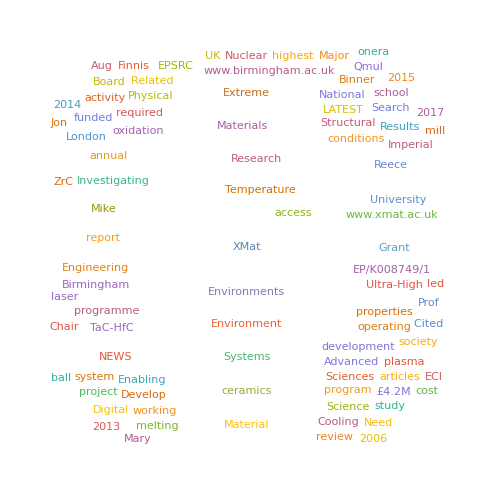

```mathematica
WordCloud@cloudData
```



```mathematica
Graphics[{Circle[{2,0}]}]
```

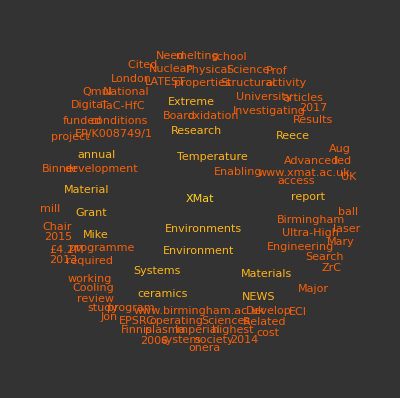

```mathematica
WordCloud[cloudData,Disk[],ImageSize->400,Background->GrayLevel[0.2],ColorFunction->ColorData[{"SolarColors",{-0.5,0.5}}]]
```

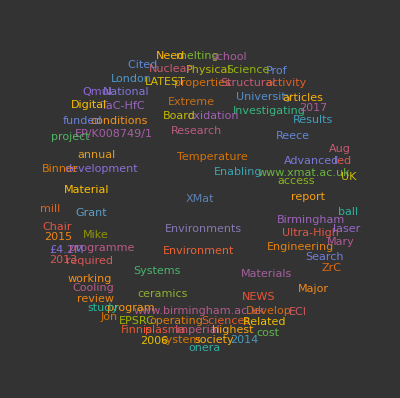

```mathematica
WordCloud[cloudData,Disk[],ImageSize->400,Background->GrayLevel[0.2]]
```

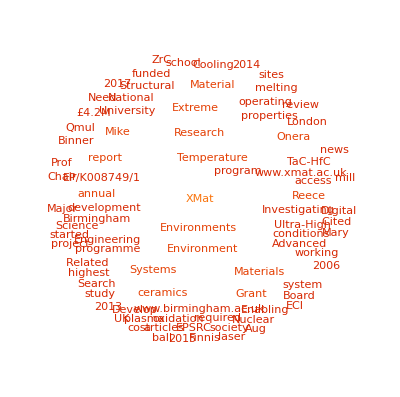

```mathematica
WordCloud[cloudData,ColorNegate@Graphics[Disk[{0,2}]],ImageSize->400,ColorFunction->ColorData[{"SolarColors",{-1,2.5}}]]
```

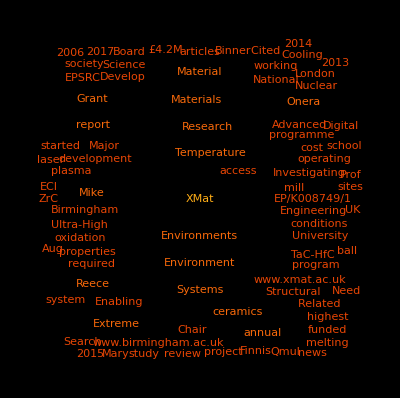

```mathematica
WordCloud[cloudData,Graphics@Square,Background->Black,ImageSize->400,ColorFunction->ColorData[{"SolarColors",{-1,1.5}}]]
```

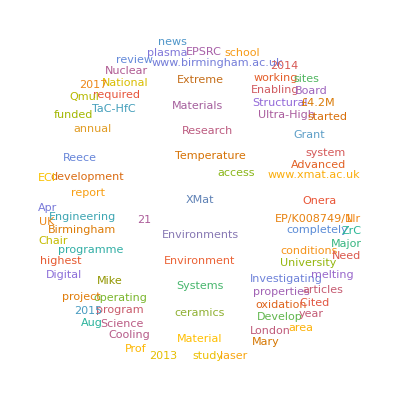

```mathematica
WordCloud@cloudData
```

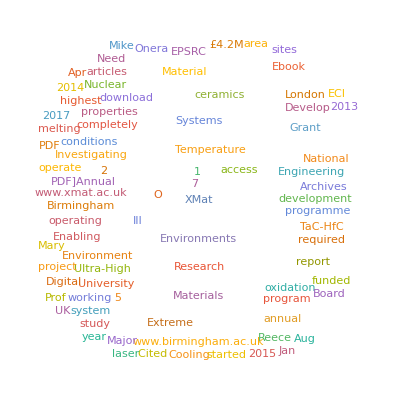

```mathematica
WordCloud@wordData
```

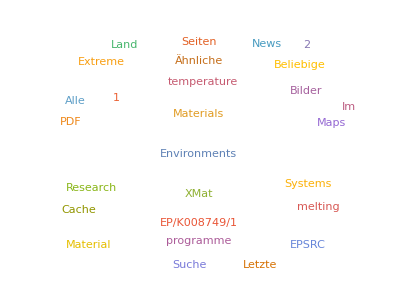

```mathematica
WordCloud@Commonest[DeleteStopwords@Flatten@TextWords@{urlin,urlin2,urlin3},30]
```

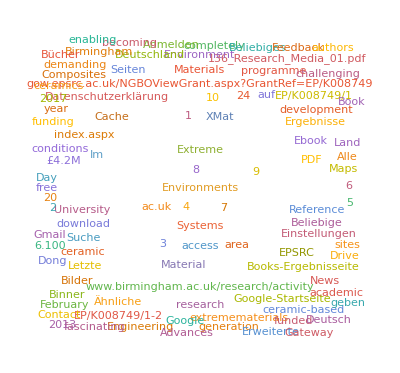

```mathematica
WordCloud@urlin
```